# ChristopherWolfram/ForeignFunctionInterface

Efficiently connect to C-compatible libraries

## Paclet Manifest

"Documentation"

"English"

"ReferencePages"

"Symbols"

"BufferToNumericArray.nb"DocumentationEnglishReferencePagesSymbolsBufferToNumericArray.nb

"BufferToString.nb"DocumentationEnglishReferencePagesSymbolsBufferToString.nb

"CallForeignFunction.nb"DocumentationEnglishReferencePagesSymbolsCallForeignFunction.nb

"CreateBuffer.nb"DocumentationEnglishReferencePagesSymbolsCreateBuffer.nb

"CreateForeignFunction.nb"DocumentationEnglishReferencePagesSymbolsCreateForeignFunction.nb

"CreateManagedExpression.nb"DocumentationEnglishReferencePagesSymbolsCreateManagedExpression.nb

"DereferenceBuffer.nb"DocumentationEnglishReferencePagesSymbolsDereferenceBuffer.nb

"FFIType.nb"DocumentationEnglishReferencePagesSymbolsFFIType.nb

"FreeBuffer.nb"DocumentationEnglishReferencePagesSymbolsFreeBuffer.nb

"GetManagedExpression.nb"DocumentationEnglishReferencePagesSymbolsGetManagedExpression.nb

"OpaqueRawPointer.nb"DocumentationEnglishReferencePagesSymbolsOpaqueRawPointer.nb

"StringToBuffer.nb"DocumentationEnglishReferencePagesSymbolsStringToBuffer.nb

"Kernel"

"Buffer.wl"KernelBuffer.wl

"ForeignFunctionInterface.wl"KernelForeignFunctionInterface.wl

"LibFFI"

"BaseTypes.wl"KernelLibFFIBaseTypes.wl

"Base.wl"KernelLibFFIBase.wl

"Constants.wl"KernelLibFFIConstants.wl

"LibFFI.wl"KernelLibFFILibFFI.wl

"RawFunctionLoading.wl"KernelLibFFIRawFunctionLoading.wl

"ManagedExpression.wl"KernelManagedExpression.wl

"OpaqueRawPointer.wl"KernelOpaqueRawPointer.wl

"LibraryResources"

"Linux-x86-64"

"ffiConstants.so"LibraryResourcesLinux-x86-64ffiConstants.so

"ForeignFunctionInterface.so"LibraryResourcesLinux-x86-64ForeignFunctionInterface.so

"libffi.a"LibraryResourcesLinux-x86-64libffi.a

"libffi.la"LibraryResourcesLinux-x86-64libffi.la

"libffi.so"LibraryResourcesLinux-x86-64libffi.so

"libffi.so.8"LibraryResourcesLinux-x86-64libffi.so.8

"libffi.so.8.1.2"LibraryResourcesLinux-x86-64libffi.so.8.1.2

"MacOSX-x86-64"

"ffiConstants.dylib"LibraryResourcesMacOSX-x86-64ffiConstants.dylib

"libffi.8.dylib"LibraryResourcesMacOSX-x86-64libffi.8.dylib

"libffi.a"LibraryResourcesMacOSX-x86-64libffi.a

"libffi.dylib"LibraryResourcesMacOSX-x86-64libffi.dylib

"libffi.la"LibraryResourcesMacOSX-x86-64libffi.la

"PacletInfo.wl"PacletInfo.wl

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

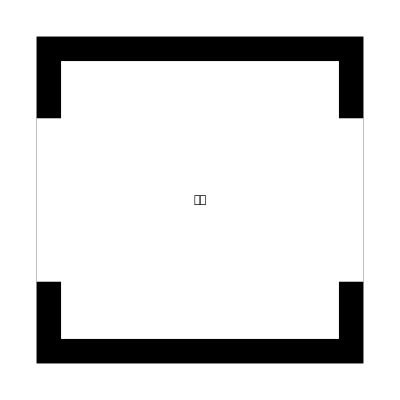

```mathematica
Graphics[{
{Black,Rectangle[{-1,-1},{1,1}],
White,Rectangle[{-0.85,-0.85},{0.85,0.85}],
Rectangle[{-1,-0.5},{1,0.5}]
},
{FontSize->Scaled[0.35],Text["𒅴𒁇"]}
},PlotRange->1,PlotRangePadding->0]
```

### Basic Description

ForeignFunctionInterface makes it possible to efficiently call functions from C-compatible libraries directly from the Wolfram Language, without the need to compile an interface layer.

### Details

This paclet uses libffi to dynamically link to C-compatible libraries at runtime

Though this paclet could be built on all platforms supported by Wolfram Language, it is currently only built for x86 macOS and Linux.

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad["/home/christopher/git/ForeignFunctionInterface/ForeignFunctionInterface"];
```

```mathematica
Needs["ChristopherWolfram`ForeignFunctionInterface`"];
```

### Basic Examples

Load a library:

```mathematica
LibraryLoad["compilerDemoBase"];
```

Create a ForeignFunctionObject referring to a function from the library:

```mathematica
addone=CreateForeignFunction["addone",{FFIType["CInt"]},FFIType["CInt"]]
```

DataStructure[ForeignFunctionObject, $Failed]

Call the foreign function:

```mathematica
CallForeignFunction[addone,{12}]
```

13

### Scope

Function calls have very little overhead:

```mathematica
LibraryLoad["compilerDemoBase"];
addone=CreateForeignFunction["addone",{FFIType["CInt"]},FFIType["CInt"]];
```

```mathematica
RepeatedTiming@CallForeignFunction[addone,{12}]
```

{3.84683×10^-7,13}

### Applications

Create a foreign function for the RAND_bytes function from OpenSSL:

```mathematica
randBytes=CreateForeignFunction["RAND_bytes",
{FFIType["OpaqueRawPointer"],FFIType["CInt"]},
FFIType["CInt"]
]
```

DataStructure[ForeignFunctionObject, $Failed]

Create a memory-managed buffer into which the random bytes can be written:

```mathematica
out=CreateManagedExpression[CreateBuffer[FFIType["UnsignedInteger8"],32],FreeBuffer]
```

DataStructure[ManagedExpression, $Failed]

Generate the random bytes:

```mathematica
CallForeignFunction[randBytes,{GetManagedExpression@out,32}]
```

1

Read the output:

```mathematica
Normal@BufferToNumericArray[GetManagedExpression@out,FFIType["UnsignedInteger8"],32]
```

{106,143,100,94,51,120,41,177,68,249,255,74,180,209,214,121,77,89,54,62,251,253,43,74,236,104,217,164,229,82,65,23}

Package into a function:

```mathematica
generateRandomBytes[len_]:=
Module[{out=CreateManagedExpression[CreateBuffer[FFIType["UnsignedInteger8"],len],FreeBuffer]},
CallForeignFunction[randBytes,{GetManagedExpression@out,len}];
BufferToNumericArray[GetManagedExpression@out,FFIType["UnsignedInteger8"],len]
]
```

```mathematica
Normal@generateRandomBytes[128]
```

{89,11,40,164,110,122,190,13,233,235,99,90,243,144,193,63,110,34,202,161,130,29,183,98,246,233,216,222,198,109,20,7,119,213,123,156,108,68,126,194,172,144,40,224,236,240,109,251,200,140,193,207,93,39,129,204,11,58,99,95,211,60,7,3,44,97,148,111,178,4,121,53,176,53,225,206,191,130,234,201,144,76,208,209,17,3,178,126,217,92,20,222,187,166,54,119,228,24,37,224,8,116,49,167,212,121,209,58,123,107,240,186,20,7,103,171,157,106,101,209,154,114,143,119,150,120,219,236}

The foreign function is very efficient:

```mathematica
RepeatedTiming[generateRandomBytes[10000000];]
```

{0.00359831,Null}

```mathematica
RepeatedTiming[RandomInteger[{0,255},10000000];]
```

{0.0339363,Null}

Create a foreign function for the SHA256 function from OpenSSL:

```mathematica
sha256=CreateForeignFunction["SHA256",
{
FFIType["OpaqueRawPointer"],
FFIType["CUnsignedLong"],
FFIType["OpaqueRawPointer"]
},
FFIType["OpaqueRawPointer"]
]
```

DataStructure[ForeignFunctionObject, $Failed]

Create a buffer containing the plaintext to hash:

```mathematica
plaintext="Hello, World!";
plaintextBuffer=CreateManagedExpression[StringToBuffer[plaintext],FreeBuffer]
```

DataStructure[ManagedExpression, $Failed]

Create a buffer into which to write the hash:

```mathematica
ciphertext=CreateManagedExpression[CreateBuffer[FFIType["UnsignedInteger8"],32],FreeBuffer]
```

DataStructure[ManagedExpression, $Failed]

Generate inputs and execute the hash:

```mathematica
CallForeignFunction[sha256,{
GetManagedExpression@plaintextBuffer,
StringLength[plaintext],
GetManagedExpression@ciphertext
}]
```

OpaqueRawPointer[…]

Extract the results:

```mathematica
Normal@BufferToNumericArray[GetManagedExpression@ciphertext,FFIType["UnsignedInteger8"],32]
```

{223,253,96,33,187,43,213,176,175,103,98,144,128,158,195,165,49,145,221,129,199,247,10,75,40,104,138,54,33,130,152,111}

Compare with the built-in function Hash:

```mathematica
Normal@Hash[plaintext,"SHA256","ByteArray"]
```

{223,253,96,33,187,43,213,176,175,103,98,144,128,158,195,165,49,145,221,129,199,247,10,75,40,104,138,54,33,130,152,111}

Package into a function:

```mathematica
generateSHA256[plaintext_]:=
Module[{
plaintextBuffer=CreateManagedExpression[StringToBuffer[plaintext],FreeBuffer],
ciphertext=CreateManagedExpression[CreateBuffer[FFIType["UnsignedInteger8"],32],FreeBuffer]
},
CallForeignFunction[sha256,{
GetManagedExpression@plaintextBuffer,
StringLength[plaintext],
GetManagedExpression@ciphertext
}];
BufferToNumericArray[GetManagedExpression@ciphertext,FFIType["UnsignedInteger8"],32]
]
```

```mathematica
generateSHA256["Hello, World!"]//Normal
```

{223,253,96,33,187,43,213,176,175,103,98,144,128,158,195,165,49,145,221,129,199,247,10,75,40,104,138,54,33,130,152,111}

The packaged function is much faster than the built-in one:

```mathematica
RepeatedTiming@Hash[plaintext,"SHA256","ByteArray"]
```

{0.000150463,ByteArray[…]}

```mathematica
RepeatedTiming@generateSHA256[plaintext]
```

{8.97923×10^-6,NumericArray[…]}

### Properties and Relations

CreateForeignFunction can create callable links to libraries much faster than custom compiling a link:

```mathematica
LibraryLoad["compilerDemoBase"];
```

```mathematica
RepeatedTiming[addone=CreateForeignFunction["addone",{FFIType["CInt"]},FFIType["CInt"]]]
```

{3.27325×10^-6,DataStructure[ForeignFunctionObject, $Failed]}

```mathematica
RepeatedTiming[addoneCf=FunctionCompile[
LibraryFunctionDeclaration["addone","compilerDemoBase",{"CInt"}->"CInt"],
Function[Typed[x,"CInt"],LibraryFunction["addone"][x]]
]]
```

{0.173684,CompiledCodeFunction[…]}

However, the custom compiled versions usually have slightly less overhead:

```mathematica
RepeatedTiming[CallForeignFunction[addone,{10}]]
```

{4.19587×10^-7,11}

```mathematica
RepeatedTiming[addoneCf[10]]
```

{1.59929×10^-7,11}

### Possible Issues

Platforms other than x86 Linux and macOS can be made to work by adding builds of libffi and the ffiConstants library (found in the source repository) to LibraryResources. Then, the linking code can be created by building the compiled component in a one-time operation:

```mathematica
BuildCompiledComponent["ForeignFunctionInterface",PacletObject["ChristopherWolfram/ForeignFunctionInterface"]]
```

Success[…]

## Source & Additional Information

### Creator

Christopher Wolfram

### Source Control Repository

https://github.com/chriswolfram/ForeignFunctionInterface

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

keyword 1

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

libffi homepage

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

WL system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

WL built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

There are some know issues with managed expressions. The design of that system will likely have to change. For example, managed expressions stored in a With are often freed before their bodies can be used:

```mathematica
With[{buf=CreateManagedExpression[foo,Echo["freed"]&]},
EchoLabel["func"][GetManagedExpression[buf]]
]
```

freed

func  foo

foo

The solution will likely be something like a ManagedBlock which will guarantee that a managed object exists for the entire body:

```mathematica
ManagedBlock[man(*a managed expression*),
man(*the body of the managed expression*)
]
```

This is still a work in progress, and there are a few missing features, though they are all relatively simple to implement. Here are some of them:

Windows support. The current platform list is just those that I can easily build for.

The ability to pass structs to and from external libraries.

The ability to create a buffer from an arbitrary NumericArray (instead of just strings).

More functions for creating and manipulating buffers / structs.